# Exercise 1.3

## Introduce a disordered interaction between next-nearest neighbours of strength W and study the band structure.

Normalizing the energy by R, the important parameter becomes the ratio W/R, which we call Μ.
Let’s start with OBC and study the bands.

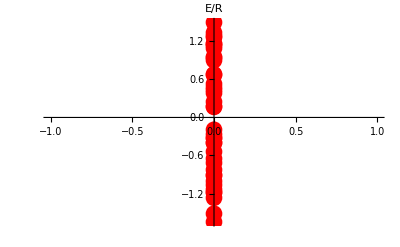

```mathematica
ClearAll;
n=20;
M=0.5;
mat=SparseArray[
Join[
Table[
{i,i+1}->RandomReal[{-1,1}],
{i,1,2n-1}
],
Table[
{i,i+2}->RandomReal[{-M,M}],
{i,1,2n-2}
]
],
{2n,2n},0.];
H=mat+Transpose[mat];
energy=Eigenvalues[H];
ListPlot[Table[{0,energy[[i]]},{i,1,2n}],
PlotStyle->{Red,PointSize[.03]},Ticks->{None,Automatic},AxesStyle->Directive[Black, 12],AxesLabel->{None,"E/R"}]
```

Let’s now study the behaviour of the band structure as a function of M in the interval [0,1]. Physically we can expect that the interaction between second neighbours is smaller than the interaction between first neighbours, that’s why we do not study the case M>1.

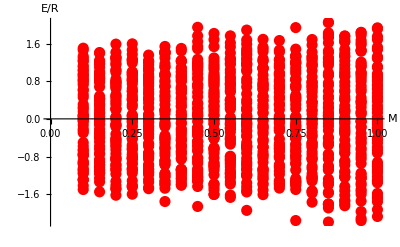

```mathematica
ClearAll;
n=30;
bands={};
For[M=0.1,M≤ 1.0,M+=0.05,
mat=SparseArray[
Join[
Table[
{i,i+1}->RandomReal[{-1,1}],
{i,1,2n-1}
],
Table[
{i,i+2}->RandomReal[{-M,M}],
{i,1,2n-2}
]
],
{2n,2n},0.];
H=mat+Transpose[mat];
energy=Eigenvalues[H];
For[i=1,i≤2n,i++,
AppendTo[bands,{M,energy[[i]]}];
]
]
ListPlot[bands,PlotStyle->{PointSize[.02],Red},AxesLabel->{"Μ","E/R"},AxesStyle->Directive[Black, 12]]
```